# Cart With Inverted Pendulum

-Graphics-

```mathematica
ClearAll["Global`*"]
$Assumptions={l>0&&k>0&&Subscript[m, 1]>0&&Subscript[m, 2]>0&&c>0&&kT>0&&cT>0}
```

{l>0&&k>0&&m_1>0&&m_2>0&&c>0&&kT>0&&cT>0}

## Lagrange’s Equations of Motion

Position vector of the mass m_2 assuming horizontal x-axis and vertical y-axis:

```mathematica
r={x[t]+l Sin[θ[t]],l Cos[θ[t]]}
```

{l Sin[θ[t]]+x[t],l Cos[θ[t]]}

Potential Energy of the System:

```mathematica
V = 1/2 k x[t]^2+Subscript[m, 2] g r[[2]]+1/2 kT θ[t]^2
```

g l Cos[θ[t]] m_2+1/2 k x[t]^2+1/2 kT θ[t]^2

Velocity of the mass m_2:

```mathematica
v = D[r,t]
```

{x'[t]+l Cos[θ[t]] θ'[t],-l Sin[θ[t]] θ'[t]}

Kinetic Energy of the System:

```mathematica
T = 1/2 Subscript[m, 1] x'[t]^2+1/2 Subscript[m, 2] v.v//Simplify//Expand
```

1/2 m_1 x'[t]^2+1/2 m_2 x'[t]^2+l Cos[θ[t]] m_2 x'[t] θ'[t]+1/2 l^2 m_2 θ'[t]^2

Virtual Work due to Dissipative and Applied Forces:

```mathematica
δW=(F[t]-c x'[t])δx-cT θ'[t]δθ + ({P[t],0}. v/.{x'[t]->δx,θ'[t]->δθ})
```

(δx+l δθ Cos[θ[t]]) P[t]+δx (F[t]-c x'[t])-cT δθ θ'[t]

Lagrangian:

```mathematica
L=T-V
```

-g l Cos[θ[t]] m_2-1/2 k x[t]^2-1/2 kT θ[t]^2+1/2 m_1 x'[t]^2+1/2 m_2 x'[t]^2+l Cos[θ[t]] m_2 x'[t] θ'[t]+1/2 l^2 m_2 θ'[t]^2

Equations of Motion:

```mathematica
eq1=D[D[L,x'[t]],t]-D[L,x[t]]==Coefficient[δW,δx]
eq2=D[D[L,θ'[t]],t]-D[L,θ[t]]==Coefficient[δW,δθ]
```

k x[t]-l Sin[θ[t]] m_2 θ'[t]^2+m_1 x''[t]+m_2 x''[t]+l Cos[θ[t]] m_2 θ''[t]==F[t]+P[t]-c x'[t]

-g l Sin[θ[t]] m_2+kT θ[t]+l Cos[θ[t]] m_2 x''[t]+l^2 m_2 θ''[t]==l Cos[θ[t]] P[t]-cT θ'[t]

## Equilibria

Equilibrium equations are obtained by setting all the time derivatives to zero in the equations of motion:

```mathematica
EqEqs={eq1,eq2}/.{θ'[t]->0,x'[t]->0,θ''[t]->0,x''[t]->0,F[t]->0,P[t]->0}
```

{k x[t]==0,-g l Sin[θ[t]] m_2+kT θ[t]==0}

Now we can solve the above for the equilibrium points:

```mathematica
Solve[EqEqs[[1]],x[t]][[1]]/.Rule->Equal
```

{x[t]==0}

```mathematica
EqTheta=Solve[EqEqs[[2]],Sin[θ[t]]][[1]]/.{Rule->Equal,θ[t]->θ}
```

{Sin[θ]==(kT θ)/(g l m_2)}

Thus, from above we see that (x,θ)  = (0,0) is one of the equilibria, but for the θ coordinate we need to solve the above transcendental equation to find possibly more equilibrium points. The solution to this nonlinear equation depends on the slope a = k_T/(g l m_2). In what follows, we plot Sin[θ] and aθ to see how many intersections (equilibria) are actually possible in this system.

```mathematica
Manipulate[Plot[{Sin[θ],a θ},{θ,-3π,3π},PlotRange->{-1.1,1.1},PlotLegends->{"Sin(θ)","kT/(g l SubscriptBox[m, 2])θ"}],{{a,0.5,"slope a"},0,3}]
```

From the figure we see that for small a there is a possibility to have an infinite number of equilibria. For only one stable equilibrium at (0,0) we need slope to be greater to one (positive stiffness):

kT/(g l m_2)>1

Lets check if for our parameters the slope is greater than one.

```mathematica
EqTheta/.{kT->10,g->9.8, l->1, Subscript[m, 2]->1}
```

{Sin[θ]==1.02041 θ}

When  kT/(g l m_2)<1, 0 equilibrium becomes unstable (negative slope/stiffness) and we acquire additional equilibria when Sinc[θ]=kT/(g l m_2) as shown in the plot below.

```mathematica
Manipulate[Plot[{Sinc[θ],a },{θ,-5π,5π},PlotRange->{-.3,1.1},PlotLegends->{"Sinc(θ)",kT/(g l Subscript[m, 2])}],{{a,0.5,"slope a"},0,1.1}]
```

This equation (Sinc[θ] = a) we can only solve when a=kT/(g l m_2)<1 , and new solutions will come in pairs. To study the stability of the additional equilibria, we consider a linearization of the equations of motion about the equilibrium point (0,θe). We need to linearize the nonlinear functions of about (0, θe) point, by considering a small motion about the θe point (θ[t]→θe+u[t], where u[t] is small angular displacement):

```mathematica
TRules={x[t]->x[t]q,x'[t]->x'[t]q,x''[t]->x''[t]q,θ[t]->θe+u[t]q,θ'[t]->u'[t]q,θ''[t]->u''[t]q,F[t]->0,P[t]->0}
```

{x[t]→q x[t],x'[t]→q x'[t],x''[t]→q x''[t],θ[t]→θe+q u[t],θ'[t]→q u'[t],θ''[t]→q u''[t],F[t]→0,P[t]→0}

```mathematica
Teqs={eq1,eq2}/.TRules
```

{k q x[t]-l q^2 Sin[θe+q u[t]] m_2 u'[t]^2+l q Cos[θe+q u[t]] m_2 u''[t]+q m_1 x''[t]+q m_2 x''[t]==-c q x'[t],-g l Sin[θe+q u[t]] m_2+kT (θe+q u[t])+l^2 q m_2 u''[t]+l q Cos[θe+q u[t]] m_2 x''[t]==-cT q u'[t]}

Now, we can do the expansion with respect to q, and them at the end set q=1:

```mathematica
LinEqs=Normal[
Series[Teqs,{q,0,1}]
]/.{q->1}
```

{k x[t]+l Cos[θe] m_2 u''[t]+m_1 x''[t]+m_2 x''[t]==-c x'[t],kT θe-g l Sin[θe] m_2+kT u[t]-g l Cos[θe] m_2 u[t]+l^2 m_2 u''[t]+l Cos[θe] m_2 x''[t]==-cT u'[t]}

```mathematica
Jsols=Solve[LinEqs,{x''[t],u''[t]}][[1]]//Simplify
```

{x''[t]→(kT θe Cos[θe]+kT Cos[θe] u[t]-g l Cos[θe] m_2 (Sin[θe]+Cos[θe] u[t])-k l x[t]+cT Cos[θe] u'[t]-c l x'[t])/(l (m_1+Sin[θe]^2 m_2)),u''[t]→1/(l^2 m_2 (m_1+Sin[θe]^2 m_2))(-m_1 (kT θe+kT u[t]-g l m_2 (Sin[θe]+Cos[θe] u[t])+cT u'[t])+m_2 (-kT θe-kT u[t]+g l m_2 (Sin[θe]+Cos[θe] u[t])+k l Cos[θe] x[t]-cT u'[t]+c l Cos[θe] x'[t]))}

Now, the Jacobian can be written as

```mathematica
JacM={{0,0,1,0},{0,0,0,1},{D[Jsols[[1,2]],x[t]],D[Jsols[[1,2]],u[t]],D[Jsols[[1,2]],x'[t]],D[Jsols[[1,2]],u'[t]]},{D[Jsols[[2,2]],x[t]],D[Jsols[[2,2]],u[t]],D[Jsols[[2,2]],x'[t]],D[Jsols[[2,2]],u'[t]]}};
JacM//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-k/(m_1+Sin[θe]^2 m_2) | (kT Cos[θe]-g l Cos[θe]^2 m_2)/(l (m_1+Sin[θe]^2 m_2)) | -c/(m_1+Sin[θe]^2 m_2) | (cT Cos[θe])/(l (m_1+Sin[θe]^2 m_2))
(k Cos[θe])/(l (m_1+Sin[θe]^2 m_2)) | (-m_1 (kT-g l Cos[θe] m_2)+m_2 (-kT+g l Cos[θe] m_2))/(l^2 m_2 (m_1+Sin[θe]^2 m_2)) | (c Cos[θe])/(l (m_1+Sin[θe]^2 m_2)) | (-cT m_1-cT m_2)/(l^2 m_2 (m_1+Sin[θe]^2 m_2)))

If any of the eigenvalues of the Jacobian have positive real part, the corresponding equilibrium is unstable. Now, we can try to evaluate these eigenvalues for (0,0) or any other equilibrium point (0,θe).

```mathematica
Eigenvalues[JacM/.{θe->0,kT->10,k->10,g->9.8, l->1, Subscript[m, 1]->1, Subscript[m, 2]->1,c->0,cT->0}]//Simplify//Chop
```

{0.+3.19437 ⅈ,0.-3.19437 ⅈ,0.+0.442721 ⅈ,0.-0.442721 ⅈ}

Thus, for (0,0) we have pure imaginary characteristic values and thus a merely stable (center) equilibrium for the given system parameters (k_T>g l m_2).

In general, we can substitute for Sin[θe]->aθe and for Cos[θe]->±√(1-a^2 θe^2) to get:

```mathematica
JacM=JacM/.{c->0,cT->0,kT->a g l Subscript[m, 2],Sin[θe]->a θe, Cos[θe]->√(1-a^2 θe^2)}//Simplify
```

{{0,0,1,0},{0,0,0,1},{-k/(m_1+a^2 θe^2 m_2),(g (-1+a^2 θe^2+a √(1-a^2 θe^2)) m_2)/(m_1+a^2 θe^2 m_2),0,0},{(k √(1-a^2 θe^2))/(l m_1+a^2 l θe^2 m_2),(g (-a+√(1-a^2 θe^2)) (m_1+m_2))/(l (m_1+a^2 θe^2 m_2)),0,0}}

Now, we can use the values given for the other parameters except k_T to get

```mathematica
JacM=JacM/.{k->10,g->9.8, l->1, Subscript[m, 1]->1, Subscript[m, 2]->1}
```

{{0,0,1,0},{0,0,0,1},{-10/(1+a^2 θe^2),(9.8 (-1+a^2 θe^2+a √(1-a^2 θe^2)))/(1+a^2 θe^2),0,0},{(10 √(1-a^2 θe^2))/(1+a^2 θe^2),(19.6 (-a+√(1-a^2 θe^2)))/(1+a^2 θe^2),0,0}}

Thus, given a we can solve for θe and determine the stability by finding characteristic values of the Jacobian. Lets, consider the case of a =kT/(g l m_2)= 0.5.

```mathematica
θeRule = Solve[Sinc[θe]==0.5,θe][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{θe→1.89549}

Since the Sinc function is symmetric, the negative of the solution above is also a solution

```mathematica
θeRule =Append[θeRule,θe->-θeRule[[1,2]]]
```

{θe→1.89549,θe→-1.89549}

```mathematica
Eigenvalues[JacM/.{a->0.5,θeRule[[1]]}]//Chop
Eigenvalues[JacM/.{a->0.5,θeRule[[2]]}]//Chop
```

{0.+2.32585 ⅈ,0.-2.32585 ⅈ,0.+1.31423 ⅈ,0.-1.31423 ⅈ}

{0.+2.32585 ⅈ,0.-2.32585 ⅈ,0.+1.31423 ⅈ,0.-1.31423 ⅈ}

We see that both new equilibria have exactly the same pure imaginary eigenvalues or characteristic values. However, for a=0.5, (0,0) becomes unstable as we acquire one positive eigenvalue as shown bellow:

```mathematica
Eigenvalues[JacM/.{a->0.5,θe->0}]//Chop
```

{0.+2.66472 ⅈ,0.-2.66472 ⅈ,2.62692,-2.62692}

Therefore, for a =0.5, (0,0) becomes unstable saddle but (0, ±1.89549) become stable center equilibria.

## Linearized equations about (0,0) and the modal analysis

```mathematica
eqs=LinEqs/.{θe->0}
```

{k x[t]+l m_2 u''[t]+m_1 x''[t]+m_2 x''[t]==-c x'[t],kT u[t]-g l m_2 u[t]+l^2 m_2 u''[t]+l m_2 x''[t]==-cT u'[t]}

Stiffness, Damping, and Mass Matrices:

```mathematica
K = Normal[CoefficientArrays[eqs,{x[t],u[t]}]][[2]]; K//MatrixForm
```

(k | 0
0 | kT-g l m_2)

```mathematica
Cc = Normal[CoefficientArrays[eqs,{x'[t],u'[t]}]][[2]]; Cc//MatrixForm
```

(c | 0
0 | cT)

```mathematica
M= Normal[CoefficientArrays[eqs,{x''[t],u''[t]}]][[2]]; M//MatrixForm
```

(m_1+m_2 | l m_2
l m_2 | l^2 m_2)

Eigensystem:

```mathematica
K = K/.{k->10,kT->10,g->9.8, l->1, Subscript[m, 1]->1, Subscript[m, 2]->1}; K//MatrixForm
M= M/.{k->10,kT->10,g->9.8, l->1, Subscript[m, 1]->1, Subscript[m, 2]->1}; M//MatrixForm
```

(10 | 0
0 | 0.2)

(2 | 1
1 | 1)

```mathematica
eigs=Eigensystem[{K,M}]
```

{{10.204,0.196002},{{-0.700074,0.71407},{-0.0203956,-0.999792}}}

Natural Frequencies and Modes:

```mathematica
ωn=Sqrt[eigs[[1]]]
NMs = eigs[[2]]
```

{3.19437,0.442721}

{{-0.700074,0.71407},{-0.0203956,-0.999792}}

Natural Modes:

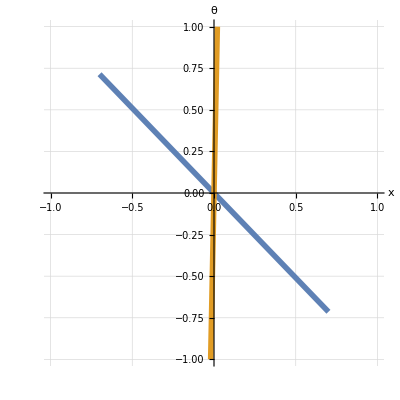

```mathematica
ListLinePlot[{{-NMs[[1]],NMs[[1]]},{-NMs[[2]],NMs[[2]]}},PlotRange->{{-1.,1.},{-1.,1.}},GridLines->Automatic,AxesLabel->{x,θ},AspectRatio->1,PlotStyle->{Thickness[0.01]}]
```

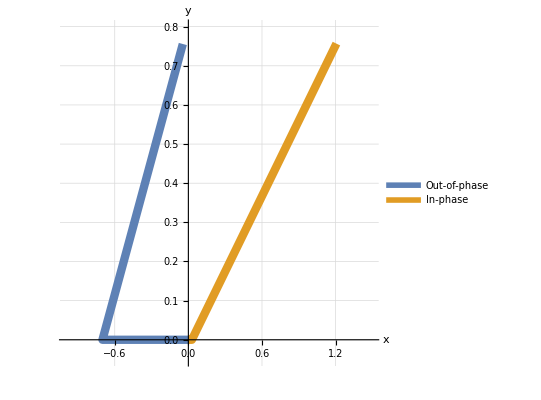

```mathematica
ListLinePlot[{{{0,0},{NMs[[1,1]],0},{NMs[[1,1]]+Sin[NMs[[1,2]]],Cos[NMs[[1,2]]]}},1.4{{0,0},{-NMs[[2,1]],0},{-NMs[[2,1]]+Sin[-NMs[[2,2]]],Cos[-NMs[[2,2]]]}}},PlotRange->{{-1,1.501},{-.05,.8}},GridLines->Automatic,AxesLabel->{x,y},AspectRatio->1,PlotStyle->{Thickness[0.015]},PlotLegends->{"Out-of-phase","In-phase"}]
```

## Free Vibration Solution

Solution can be written as a linear combination of all modal solutions:

```mathematica
Sol=a NMs[[1]]Cos[ωn[[1]]t+ϕ]+b NMs[[2]]Cos[ωn[[2]]t+ψ]
```

{-0.700074 a Cos[3.19437 t+ϕ]-0.0203956 b Cos[0.442721 t+ψ],0.71407 a Cos[3.19437 t+ϕ]-0.999792 b Cos[0.442721 t+ψ]}

Now we apply the initial conditions to find the unknown amplitudes and the phases:

```mathematica
iceqs=Simplify[Join[Thread[(Sol/.t->0)==0],Thread[(D[Sol,t]/.t->0)=={0,ω0}]]]
```

{1. a Cos[ϕ]+0.0291335 b Cos[ψ]==0,1. a Cos[ϕ]==1.40013 b Cos[ψ],1. a Sin[ϕ]+0.00403773 b Sin[ψ]==0,-2.281 a Sin[ϕ]+0.442629 b Sin[ψ]==ω0}

```mathematica
coeffs=Solve[iceqs,{a,b,ϕ,ψ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→-0.00893621 ω0,b→-2.21318 ω0,ϕ→1.5708,ψ→-1.5708},{a→0.00893621 ω0,b→-2.21318 ω0,ϕ→-1.5708,ψ→-1.5708},{a→-0.00893621 ω0,b→2.21318 ω0,ϕ→1.5708,ψ→1.5708},{a→0.00893621 ω0,b→2.21318 ω0,ϕ→-1.5708,ψ→1.5708}}

All of the solutions above represent the same amplitudes and the phases due to the Sin and Cos symmetries. Thus, if we only focus on positive amplitudes, we get:

```mathematica
Sol1=Sol/.coeffs[[4]]
```

{-0.00625601 ω0 Cos[1.5708-3.19437 t]-0.0451391 ω0 Cos[1.5708+0.442721 t],0.00638108 ω0 Cos[1.5708-3.19437 t]-2.21272 ω0 Cos[1.5708+0.442721 t]}

Finally, we plot the free response

```mathematica
Manipulate[Plot[Evaluate[Sol1/.{ω0->s}],{t,0,50},PlotStyle->{Thickness[0.01]},GridLines->Automatic],{{s,1,"ω_0"},0,10}]
```

```mathematica
D[Sin[z]Cos[x],{{z,x}}]
```

{Cos[x] Cos[z],-Sin[x] Sin[z]}